```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210628_finalising/fxd_coefficients"];
```

Fixed Coefficients (Initial Obj. Func. Term Series)

Objective Function, Interval: (2,4), bounds: {5, 250}, term amounts: {105, doubled, quadrupled}

Data Input

```mathematica
case="coeffs";
{a1,a2,a3}={"250","105","(2,4)"};
{b1,b2,b3}={"250","quadrupled","(2,4)"};
{c1,c2,c3}={"5","105","(2,4)"};
{d1,d2,d3}={"5","doubled","(2,4)"};
{e1,e2,e3}={"5","quadrupled","(2,4)"};
{a,b,c,d,e}={"-"<>a1<>"+"<>a1<>"_"<>a2<>"_"<>a3,"-"<>b1<>"+"<>b1<>"_"<>b2<>"_"<>b3,"-"<>c1<>"+"<>c1<>"_"<>c2<>"_"<>c3,"-"<>d1<>"+"<>d1<>"_"<>d2<>"_"<>d3,"-"<>e1<>"+"<>e1<>"_"<>e2<>"_"<>e3};
```

```mathematica
modularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-modularityvalues-fss.mx"];
modularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-modularityvalues-fss.mx"];
modularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-modularityvalues-fss.mx"];
modularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-modularityvalues-fss.mx"];
modularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-modularityvalues-fss.mx"];

modularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-modularityvalues-fbs.mx"];
modularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-modularityvalues-fbs.mx"];
modularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-modularityvalues-fbs.mx"];
modularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-modularityvalues-fbs.mx"];
modularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-zscores-fss.mx"];
zscores2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-zscores-fss.mx"];
zscores3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-zscores-fss.mx"];
zscores4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-zscores-fss.mx"];
zscores5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-zscores-fss.mx"];

zscores1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-zscores-fbs.mx"];
zscores2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-zscores-fbs.mx"];
zscores3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-zscores-fbs.mx"];
zscores4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-zscores-fbs.mx"];
zscores5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvaluesS={Thread[{deletionrange,modularityvalues1s}],Thread[{deletionrange,modularityvalues2s}],Thread[{deletionrange,modularityvalues3s}],Thread[{deletionrange,modularityvalues4s}],Thread[{deletionrange,modularityvalues5s}]};
modularityvaluesB={Thread[{deletionrange,modularityvalues1b}],Thread[{deletionrange,modularityvalues2b}],Thread[{deletionrange,modularityvalues3b}],Thread[{deletionrange,modularityvalues4b}],Thread[{deletionrange,modularityvalues5b}]};
```

```mathematica
singlerandommodularityvaluesS={Thread[{deletionrange,singlerandomerdrenmodularityvalues1s}],Thread[{deletionrange,singlerandomcommmodularityvalues1s}],Thread[{deletionrange,singlerandomerdrenmodularityvalues2s}],Thread[{deletionrange,singlerandomcommmodularityvalues2s}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues3s}],
Thread[{deletionrange,singlerandomcommmodularityvalues3s}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues4s}],Thread[{deletionrange,singlerandomcommmodularityvalues4s}],Thread[{deletionrange,singlerandomerdrenmodularityvalues5s}],Thread[{deletionrange,singlerandomcommmodularityvalues5s}]};
singlerandommodularityvaluesB={Thread[{deletionrange,singlerandomerdrenmodularityvalues1b}],Thread[{deletionrange,singlerandomcommmodularityvalues1b}],Thread[{deletionrange,singlerandomerdrenmodularityvalues2b}],Thread[{deletionrange,singlerandomcommmodularityvalues2b}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues3b}],
Thread[{deletionrange,singlerandomcommmodularityvalues3b}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues4b}],Thread[{deletionrange,singlerandomcommmodularityvalues4b}],Thread[{deletionrange,singlerandomerdrenmodularityvalues5b}],Thread[{deletionrange,singlerandomcommmodularityvalues5b}]};
```

```mathematica
zscoresS={Thread[{deletionrange,zscores1s[[All,1]]}],Thread[{deletionrange,zscores1s[[All,2]]}],Thread[{deletionrange,zscores2s[[All,1]]}],Thread[{deletionrange,zscores2s[[All,2]]}],Thread[{deletionrange,zscores3s[[All,1]]}],Thread[{deletionrange,zscores3s[[All,2]]}],Thread[{deletionrange,zscores4s[[All,1]]}],Thread[{deletionrange,zscores4s[[All,2]]}],Thread[{deletionrange,zscores5s[[All,1]]}],Thread[{deletionrange,zscores5s[[All,2]]}]};
zscoresB={Thread[{deletionrange,zscores1b[[All,1]]}],Thread[{deletionrange,zscores1b[[All,2]]}],Thread[{deletionrange,zscores2b[[All,1]]}],Thread[{deletionrange,zscores2b[[All,2]]}],Thread[{deletionrange,zscores3b[[All,1]]}],Thread[{deletionrange,zscores3b[[All,2]]}],Thread[{deletionrange,zscores4b[[All,1]]}],Thread[{deletionrange,zscores4b[[All,2]]}],Thread[{deletionrange,zscores5b[[All,1]]}],Thread[{deletionrange,zscores5b[[All,2]]}]};
```

Plots

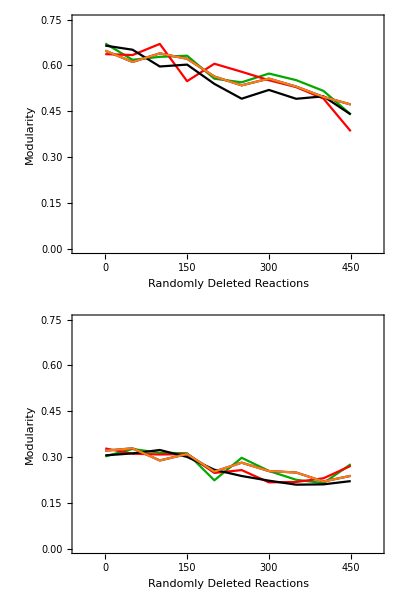
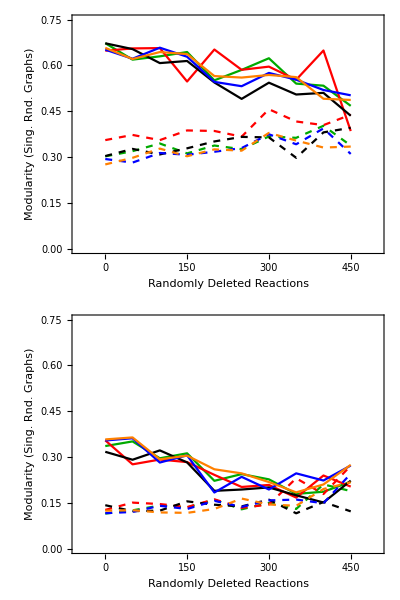
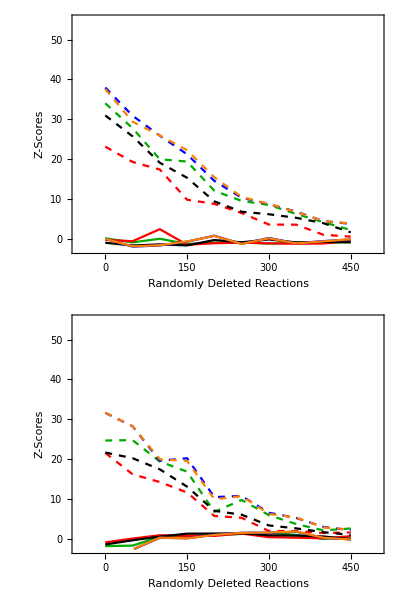

```mathematica
padding=38;
modularityplotrange={0,0.75};
xaxisplotrange={-50,500};
zscorerange={-2.5,55};
Row[{
Column[{ListLinePlot[modularityvaluesS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvaluesB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvaluesS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvaluesB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscoresS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}],ListLinePlot[zscoresB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}]}]
,Column[{LineLegend[{Darker@Green,Red,Black,Blue,Orange},{"[-"<>a1<>","<>a1<>"] -> "<>a2,"[-"<>b1<>","<>b1<>"] -> "<>b2,"[-"<>c1<>","<>c1<>"] -> "<>c2,"[-"<>d1<>","<>d1<>"] -> "<>d2,"[-"<>e1<>","<>e1<>"] -> "<>e2},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Constrained\nBound Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

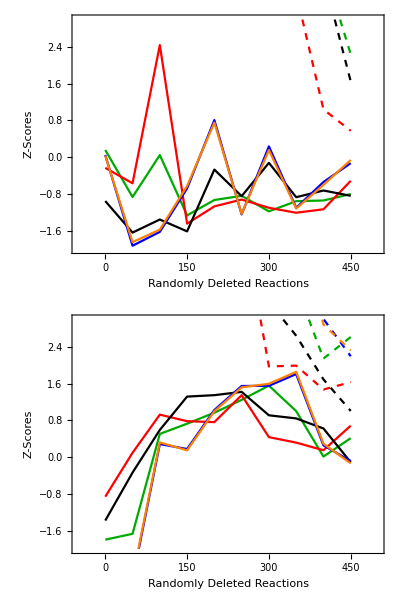

```mathematica
Column[{ListLinePlot[zscoresS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscoresB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function, Interval: (-1,1), bounds: {5, 250}, term amounts: {105, doubled, quadrupled}

Data Input

```mathematica
case="coeffs";
{a1,a2,a3}={"250","105","(-1,1)"};
{b1,b2,b3}={"250","quadrupled","(-1,1)"};
{c1,c2,c3}={"5","105","(-1,1)"};
{d1,d2,d3}={"5","doubled","(-1,1)"};
{e1,e2,e3}={"5","quadrupled","(-1,1)"};
{a,b,c,d,e}={"-"<>a1<>"+"<>a1<>"_"<>a2<>"_"<>a3,"-"<>b1<>"+"<>b1<>"_"<>b2<>"_"<>b3,"-"<>c1<>"+"<>c1<>"_"<>c2<>"_"<>c3,"-"<>d1<>"+"<>d1<>"_"<>d2<>"_"<>d3,"-"<>e1<>"+"<>e1<>"_"<>e2<>"_"<>e3};
```

```mathematica
modularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-modularityvalues-fss.mx"];
modularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-modularityvalues-fss.mx"];
modularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-modularityvalues-fss.mx"];
modularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-modularityvalues-fss.mx"];
modularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-modularityvalues-fss.mx"];

modularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-modularityvalues-fbs.mx"];
modularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-modularityvalues-fbs.mx"];
modularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-modularityvalues-fbs.mx"];
modularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-modularityvalues-fbs.mx"];
modularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores1s=Import["plot_values/fxd_"<>case<>"/"<>a<>"-zscores-fss.mx"];
zscores2s=Import["plot_values/fxd_"<>case<>"/"<>b<>"-zscores-fss.mx"];
zscores3s=Import["plot_values/fxd_"<>case<>"/"<>c<>"-zscores-fss.mx"];
zscores4s=Import["plot_values/fxd_"<>case<>"/"<>d<>"-zscores-fss.mx"];
zscores5s=Import["plot_values/fxd_"<>case<>"/"<>e<>"-zscores-fss.mx"];

zscores1b=Import["plot_values/fxd_"<>case<>"/"<>a<>"-zscores-fbs.mx"];
zscores2b=Import["plot_values/fxd_"<>case<>"/"<>b<>"-zscores-fbs.mx"];
zscores3b=Import["plot_values/fxd_"<>case<>"/"<>c<>"-zscores-fbs.mx"];
zscores4b=Import["plot_values/fxd_"<>case<>"/"<>d<>"-zscores-fbs.mx"];
zscores5b=Import["plot_values/fxd_"<>case<>"/"<>e<>"-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvaluesS={Thread[{deletionrange,modularityvalues1s}],Thread[{deletionrange,modularityvalues2s}],Thread[{deletionrange,modularityvalues3s}],Thread[{deletionrange,modularityvalues4s}],Thread[{deletionrange,modularityvalues5s}]};
modularityvaluesB={Thread[{deletionrange,modularityvalues1b}],Thread[{deletionrange,modularityvalues2b}],Thread[{deletionrange,modularityvalues3b}],Thread[{deletionrange,modularityvalues4b}],Thread[{deletionrange,modularityvalues5b}]};
```

```mathematica
singlerandommodularityvaluesS={Thread[{deletionrange,singlerandomerdrenmodularityvalues1s}],Thread[{deletionrange,singlerandomcommmodularityvalues1s}],Thread[{deletionrange,singlerandomerdrenmodularityvalues2s}],Thread[{deletionrange,singlerandomcommmodularityvalues2s}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues3s}],
Thread[{deletionrange,singlerandomcommmodularityvalues3s}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues4s}],Thread[{deletionrange,singlerandomcommmodularityvalues4s}],Thread[{deletionrange,singlerandomerdrenmodularityvalues5s}],Thread[{deletionrange,singlerandomcommmodularityvalues5s}]};
singlerandommodularityvaluesB={Thread[{deletionrange,singlerandomerdrenmodularityvalues1b}],Thread[{deletionrange,singlerandomcommmodularityvalues1b}],Thread[{deletionrange,singlerandomerdrenmodularityvalues2b}],Thread[{deletionrange,singlerandomcommmodularityvalues2b}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues3b}],
Thread[{deletionrange,singlerandomcommmodularityvalues3b}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues4b}],Thread[{deletionrange,singlerandomcommmodularityvalues4b}],Thread[{deletionrange,singlerandomerdrenmodularityvalues5b}],Thread[{deletionrange,singlerandomcommmodularityvalues5b}]};
```

```mathematica
zscoresS={Thread[{deletionrange,zscores1s[[All,1]]}],Thread[{deletionrange,zscores1s[[All,2]]}],Thread[{deletionrange,zscores2s[[All,1]]}],Thread[{deletionrange,zscores2s[[All,2]]}],Thread[{deletionrange,zscores3s[[All,1]]}],Thread[{deletionrange,zscores3s[[All,2]]}],Thread[{deletionrange,zscores4s[[All,1]]}],Thread[{deletionrange,zscores4s[[All,2]]}],Thread[{deletionrange,zscores5s[[All,1]]}],Thread[{deletionrange,zscores5s[[All,2]]}]};
zscoresB={Thread[{deletionrange,zscores1b[[All,1]]}],Thread[{deletionrange,zscores1b[[All,2]]}],Thread[{deletionrange,zscores2b[[All,1]]}],Thread[{deletionrange,zscores2b[[All,2]]}],Thread[{deletionrange,zscores3b[[All,1]]}],Thread[{deletionrange,zscores3b[[All,2]]}],Thread[{deletionrange,zscores4b[[All,1]]}],Thread[{deletionrange,zscores4b[[All,2]]}],Thread[{deletionrange,zscores5b[[All,1]]}],Thread[{deletionrange,zscores5b[[All,2]]}]};
```

Plots

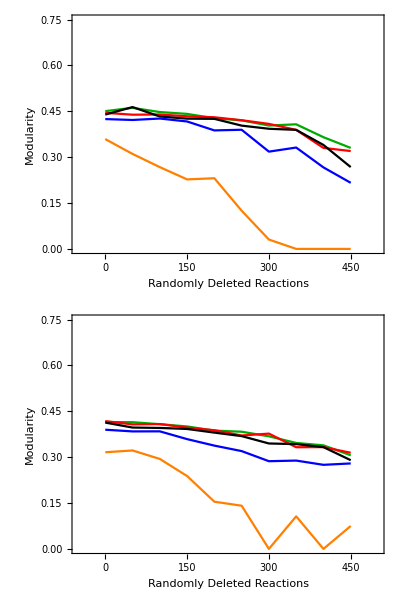
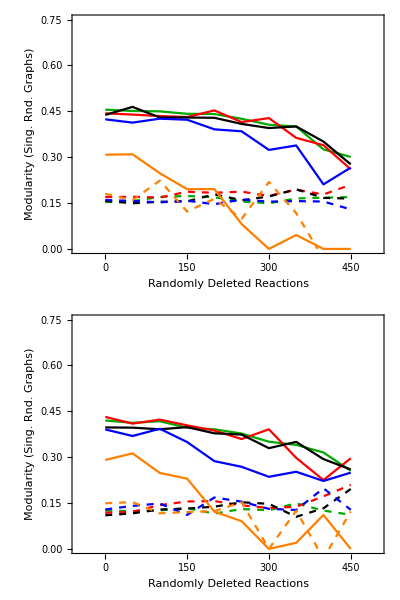
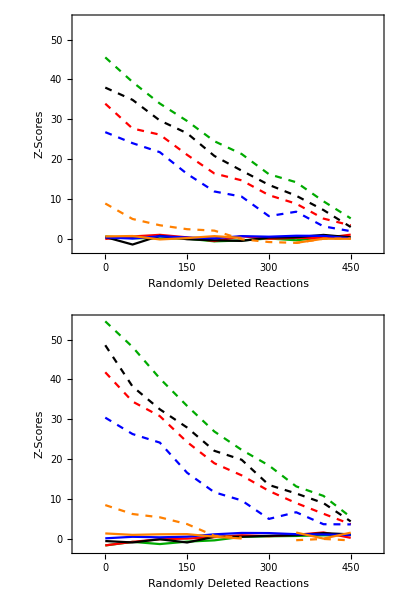

```mathematica
padding=38;
modularityplotrange={0,0.75};
xaxisplotrange={-50,500};
zscorerange={-2.5,55};
Row[{
Column[{ListLinePlot[modularityvaluesS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvaluesB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvaluesS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvaluesB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscoresS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}],ListLinePlot[zscoresB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}]}]
,Column[{LineLegend[{Darker@Green,Red,Black,Blue,Orange},{"[-"<>a1<>","<>a1<>"] -> "<>a2,"[-"<>b1<>","<>b1<>"] -> "<>b2,"[-"<>c1<>","<>c1<>"] -> "<>c2,"[-"<>d1<>","<>d1<>"] -> "<>d2,"[-"<>e1<>","<>e1<>"] -> "<>e2},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Constrained\nBound Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

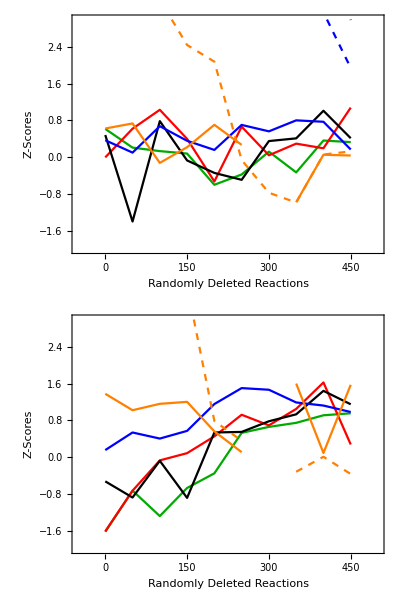

```mathematica
Column[{ListLinePlot[zscoresS,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscoresB,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```